```mathematica
sq[n_,k_] := Floor[ n^k]-Floor[(n-1)^k]
```

```mathematica
Table[sq[n,2/3],{n,1,30}]
```

{1,0,1,0,0,1,0,1,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0}

```mathematica
Clear[dd,aa]
dd[n_, t_,k_] := dd[n,t,k]=Sum[ dd[n/(j^(1/t)),t,k-1],{j,2,n^t}]
dd[n_, t_,0]:=UnitStep[n-1]
ld[n_,t_] := Sum[ (-1)^(k+1)/k dd[n,t,k],{k,1,Log2@n}]
aa[n_, t_,k_] := aa[n,t,k]=Sum[aa[Floor[n/j],t,k-1],{j,1,Floor[n^t]}]-aa[n,t,k-1]
aa[n_, t_,0]:=UnitStep[n-1]
la[n_,t_] := Sum[ (-1)^(k+1)/k aa[n,t,k],{k,1,Log2@n}]
```

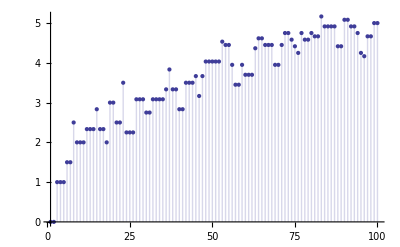

```mathematica
DiscretePlot[la[n,2/3],{n,1,100}]
```

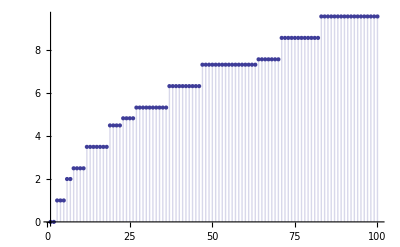

```mathematica
DiscretePlot[{ld[n,2/3]},{n,1,100}]
```

```mathematica
DiscretePlot[{ld[Floor[n^(2/3)],1]},{n,1,100}]
```

-Graphics-

```mathematica
dd[100,2/3,2]
```

27

```mathematica
Sum[ 1,{j,2,Floor[100^(2/3)]},{k,2,Floor[100^(2/3)/j]}]
```

29

```mathematica
dd[100,2/3,2]
```

27

```mathematica
dd[Floor[100^(2/3)],1,2]
```

29

```mathematica
Floor[100^(2/3)]
```

21

```mathematica
Grid@Table[ 1,{j,2,21},{k,2,21/j}]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 |  |  | 
1 | 1 | 1 | 1 |  |  |  |  | 
1 | 1 | 1 |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  | 
1 |  |  |  |  |  |  |  | 
1 |  |  |  |  |  |  |  | 
1 |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |

```mathematica
16*6
```

96

```mathematica
sq[15,2/3]
```

1

```mathematica
sq[6,2/3]
```

1

```mathematica
Table[ sq[j,2/3],{j,1,16}]
```

{1,0,1,0,0,1,0,1,0,0,0,1,0,0,1,0}

```mathematica
dd[16,2/3,1]
```

5

```mathematica
dd[21/3,1,1]
```

6

```mathematica
N[16^(2/3)]
```

6.3496

```mathematica
Floor[100^(2/3)]/3
```

7

```mathematica
Floor[30^(2/3)]
```

9

```mathematica
1^(3/2) 9^(3/2)
```

27

```mathematica
Floor[(30)^(2/3)/3]
```

3

```mathematica
N[3^(3/2) 3^(3/2)]
```

27.

```mathematica
Sum[ 1,{j,2,Floor[100^(2/3)]},{k,2,(100/j^(3/2))^(2/3)}]
```

29

```mathematica
Clear[dd]
dd[n_, p_,q_,k_] := dd[n,p,q,k]=Sum[ dd[n/(j^(1/p) j2^(1/q)),p,q,k-1],{j,1,Floor[n^p]}, {j2,1,Floor[(n/j^(1/p))^q]}]
dd[n_, p_,q_,0]:=UnitStep[n-1]
d2[n_, p_, q_, k_] := Sum[ (-1)^(k-j)Binomial[k,j]dd[n,p,q,j],{j,0,k}]
ld[n_,p_,q_] := Sum[ (-1)^(k+1)/k d2[n,N@Log[p]/Log[n],N@Log[q]/Log[n],k],{k,1,Log2@n}]
pr[n_] := Sum[ PrimePi[ n^(1/k)]/k,{k,1,Log2@n}]
```

```mathematica
ld[100,70,60]
```

212/5

```mathematica
pr[ 70]+pr[60]
```

212/5

```mathematica
dd[100,1,1,1]
```

482

```mathematica
Sum[ 1,{j,2,100},{k,2,100/j},{l,2,100/(j k)}]
```

324

```mathematica
d2[100,1,1,2]
```

2612

0.922549

```mathematica
Sum[ 1,{j,1,100},{k,1,(100/j)^Log[100,70]}]
```

388

```mathematica
Sum[ 1,{j,1,70},{k,1,(70/j)^Log[70,100]}]
```

388

```mathematica
Clear[dz]
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=dz[n,z]=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}]
Dz[n_,z_] := Sum[ dz[j,z],{j,1,n}]
```

```mathematica
dd[100,1,N@Log[70]/Log[100],1]
```

387

```mathematica
Sum[ 1,{j,1,100^1}, {j2,1,Floor[(100/j^(1/1))^(N@Log[70]/Log[100])]}]
```

387

```mathematica
(* Recursive Form *)
Clear[dd,d2a]
dd[n_, q_,k_] := dd[n,q,k]=Sum[ dd[n/(j j2^(1/q)),q,k-1],{j,1,Floor[n]}, {j2,1,Floor[(n/j)^q]}]
dd[n_, q_,0]:=UnitStep[n-1]
d2[n_,  q_, k_] := Sum[ (-1)^(k-j)Binomial[k,j]dd[n,q,j],{j,0,k}]
d2a[n_, q_,k_] := d2a[n,q,k]=Sum[ d2a[n/(j j2^(1/q)),q,k-1],{j,1,Floor[n]}, {j2,1,Floor[(n/j)^q]}]-d2a[n,q,k-1]
d2a[n_, q_,0]:=UnitStep[n-1]
ld[n_,q_] := Sum[ (-1)^(k+1)/k d2a[n,N@Log[q]/Log[n],k],{k,1,Log2@n}]
pr[n_] := Sum[ PrimePi[ n^(1/k)]/k,{k,1,Log2@n}]
```

```mathematica
ld[100,70]
```

3049/60

```mathematica
pr[100]+pr[70]
```

3049/60

```mathematica
Sum[ 1, {a,1,100},{b,1,Floor[100/a]},{c,1,Floor[(100/(a b))^(N@Log[100,70])]},{d,1,Floor[(100/(a b c^(N@Log[70,100])))^N@(Log[100,70])]}]
```

2702

```mathematica
dd[100,N@Log[100,70],2]
```

2699

```mathematica
Sum[ 1, {a,1,100},{c,1,Floor[(100/(a ))^(N@Log[100,70])]}]
```

387

```mathematica
Sum[ 1, {a,1,Floor[100]},{c,1,Floor[(100/a)^(ll=N@Log[100,70])]},{b,1,Floor[100/(a c^(1/ll))]},{d,1,Floor[(100/(a b c^(1/ll)))^ll]}]
```

2699

```mathematica
Sum[ 1, {a,1,Floor[100]},{b,1,Floor[100/a]},{c,1,Floor[(100/(a b))^(ll=N@Log[100,70])]},{d,1,Floor[(100/(a b c^(1/ll)))^ll]}]
```

2699

```mathematica
Sum[ dz[a,2], {a,1,Floor[100]},{c,1,Floor[(100/(a))^(ll=N@Log[100,70])]},{d,1,Floor[(100/(a c^(1/ll)))^ll]}]
```

2699

```mathematica
Sum[ dz[a,2]dz[c,2], {a,1,Floor[100]},{c,1,Floor[(100/a)^(N@Log[100,70])]}]
```

2699

```mathematica
Sum[ dz[a,3]dz[c,3], {a,1,Floor[100]},{c,1,Floor[(100/a)^(N@Log[100,70])]}]
```

10319

```mathematica
dd[100,N@Log[100,70],3]
```

10319

```mathematica
Sum[ dz[a,5]dz[c,5], {a,1,Floor[100]},{c,1,Floor[(100/a)^(N@Log[100,70])]}]
```

69103

```mathematica
dd[100,N@Log[100,70],5]
```

69103

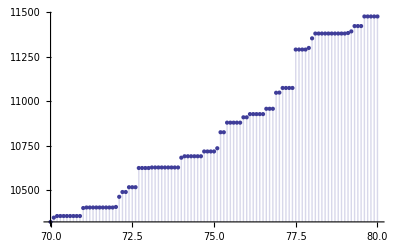

```mathematica
DiscretePlot[ dd[100,N@Log[100,y],3],{y,70,80,.1}]
```

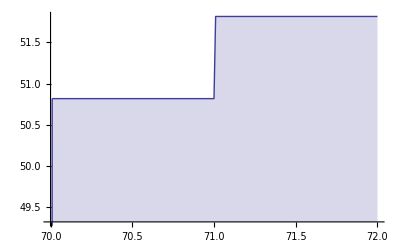

```mathematica
DiscretePlot[ ld[100,y],{y,70,72,.01}]
```

```mathematica
(* Form relying on dz *)
Clear[dd]
Clear[dz]
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=dz[n,z]=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}]
Dz[n_,z_] := Sum[ dz[j,z],{j,1,n}]
dd[n_, q_,z_] := dd[n,q,z]=Sum[ dz[a,z]dz[b,z],{a,1,Floor[n]}, {b,1,Floor[(n/a)^q]}]
d2[n_,  q_, k_] := Sum[ (-1)^(k-j)Binomial[k,j]dd[n,q,j],{j,0,k}]
ld[n_,q_] := Sum[ (-1)^(k+1)/k d2[n,N@Log[q]/Log[n],k],{k,1,Log2@n}]
pr[n_] := Sum[ PrimePi[ n^(1/k)]/k,{k,1,Log2@n}]
```

```mathematica
ld[100,70]
```

3049/60

```mathematica
pr[100]+pr[70]
```

3049/60

```mathematica
(* Inverse? *)
Clear[dd]
Clear[dz]
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=dz[n,z]=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}]
Dz[n_,z_] := Sum[ dz[j,z],{j,1,n}]
dd[n_, q_,z_] := dd[n,q,z]=Sum[ dz[a,z]dz[b,-z],{a,1,Floor[n]}, {b,1,Floor[(n/a)^q]}]
d2[n_,  q_, k_] := Sum[ (-1)^(k-j)Binomial[k,j]dd[n,q,j],{j,0,k}]
ld[n_,q_] := Sum[ (-1)^(k+1)/k d2[n,N@Log[q]/Log[n],k],{k,1,Log2@n}]
pr[n_] := Sum[ PrimePi[ n^(1/k)]/k,{k,1,Log2@n}]
```

```mathematica
ld[1000,170]
```

47767/360

```mathematica
(* Inverse!!!!!! *)
pr[1000]-pr[170]
```

47767/360

```mathematica
(* Generalize? *)
Clear[dd]
Clear[dz]
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=dz[n,z]=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}]
Dz[n_,z_] := Sum[ dz[j,z],{j,1,n}]
dd[n_, q_,z_,s_,t_] := dd[n,q,z,s,t]=Sum[ dz[a,z s]dz[b,z t],{a,1,Floor[n]}, {b,1,Floor[(n/a)^q]}]
d2[n_,  q_, k_,s_,t_] := Sum[ (-1)^(k-j)Binomial[k,j]dd[n,q,j,s,t],{j,0,k}]
ld[n_,q_,s_,t_] := Sum[ (-1)^(k+1)/k d2[n,N@Log[q]/Log[n],k,s,t],{k,1,Log2@n}]
pr[n_] := Sum[ PrimePi[ n^(1/k)]/k,{k,1,Log2@n}]
```

```mathematica
ld[1000,170,3,4]
```

5649/8

```mathematica
(* Generalize!!! *)
3pr[1000]+4pr[170]
```

5649/8

```mathematica
(* j^-s Form? *)
Clear[dda]
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=dz[n,z]=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}]
Dz[n_,z_] := Sum[ dz[j,z],{j,1,n}]
dda[n_, s_,q_,z_] := dda[n,s,q,z]=Sum[a^-s b^-s dz[a,z]dz[b,z],{a,1,Floor[n]}, {b,1,Floor[(n/a)^q]}]
dd[n_,s_, q_,k_] := dd[n,s,q,k]=Sum[ j^-s j2^-s dd[n/(j j2^(1/q)),s,q,k-1],{j,1,Floor[n]}, {j2,1,Floor[(n/j)^q]}]
dd[n_,s_, q_,0]:=UnitStep[n-1]
d2[n_, s_, q_, k_] := Sum[ (-1)^(k-j)Binomial[k,j]dda[n,s,q,j],{j,0,k}]
ld[n_,s_,q_] := Sum[ (-1)^(k+1)/k d2[n,s,N@Log[q]/Log[n],k],{k,1,Log2@n}]
pr[n_,s_] := Sum[ FullSimplify[MangoldtLambda[j]/Log[j]] j^-s,{j,2,n}]
ch[n_] := -Sum[MangoldtLambda[j],{j,2,n}]
(* j^-s Form! *)
```

```mathematica
ld[100,0,70]
```

3049/60

```mathematica
pr[100,0]+pr[70,0]
```

3049/60

```mathematica
N[D[ld[100,s,70],s]/.s->0]
```

-160.587

```mathematica
N[D[pr[100,s]+pr[70,s],s]/.s->0]
```

-160.587

```mathematica
N[ch[100]+ch[70]]
```

-160.587

```mathematica
Clear[dd,d2a,d2b]
dd[n_, q_,k_] := dd[n,q,k]=Sum[ dd[n/(j j2^(1/q)),q,k-1],{j,1,Floor[n]}, {j2,1,Floor[(n/j)^q]}]
dd[n_, q_,0]:=UnitStep[n-1]
d2a[n_, q_,k_] := d2a[n,q,k]=Sum[ d2a[n/(j j2^(1/q)),q,k-1],{j,1,Floor[n]}, {j2,1,Floor[(n/j)^q]}]-d2a[n, q,k-1]
d2a[n_, q_,0]:=UnitStep[n-1]
d2b[n_, q_,k_] := d2b[n,q,k]=Sum[ d2b[n/(j j2^(1/q)),q,k-1],{j,2,Floor[n]}, {j2,2,Floor[(n/j)^q]}]+Sum[ d2b[n/j ,q,k-1],{j,2,Floor[n]}]+Sum[ d2b[n/j2^(1/q),q,k-1], {j2,2,Floor[n^q]}]
d2b[n_, q_,0]:=UnitStep[n-1]
d2[n_,  q_, k_] := Sum[ (-1)^(k-j)Binomial[k,j]dd[n,q,j],{j,0,k}]
ld[n_,q_] := Sum[ (-1)^(k+1)/k d2[n,N@Log[q]/Log[n],k],{k,1,Log2@n}]
pr[n_] := Sum[ PrimePi[ n^(1/k)]/k,{k,1,Log2@n}]
```

```mathematica
d2b[100,N[Log[100,70]],3]
```

3382

```mathematica
d2[100,N[Log[100,70]],3]
```

3382

```mathematica
d2a[100,N[Log[100,70]],3]
```

3382

```mathematica
p q - 1
```

-1+p q

```mathematica
bb = p q - 1
```

-1+p q

```mathematica
Expand[aa - bb]
```

2-p-q

```mathematica
Expand[(p-1)(q-1) + (p-1) + (q-1)]
```

-1+p q